```mathematica
Sigma[0] = IdentityMatrix[2]
Sigma[1] = {{0, 1}, {1, 0}}
Sigma[2] = {{0, -I}, {I, 0}}
Sigma[3] = {{1, 0}, {0, -1}}
SigmaP= (Sigma[1]+ I*Sigma[2])/2
SigmaM= (Sigma[1]- I*Sigma[2])/2
```

{{1,0},{0,1}}

{{0,1},{1,0}}

{{0,-ⅈ},{ⅈ,0}}

{{1,0},{0,-1}}

{{0,1},{0,0}}

{{0,0},{1,0}}

```mathematica
FullSigma[ j_, k_, nQubit_]:=KroneckerProduct[IdentityMatrix[2^(j-1)], Sigma[k], IdentityMatrix[2^(nQubit-j)]]
MatrixForm[FullSigma[1, 3, 2]]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

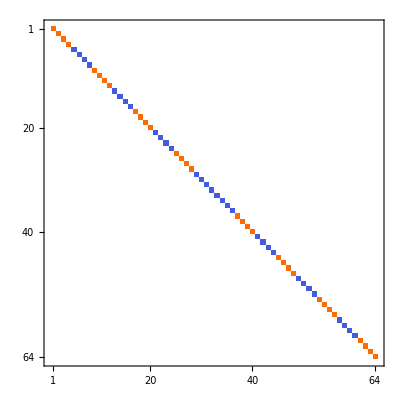

```mathematica
H1s[j_, s_, nQubit_] := FullSigma[3*(s-1)+j, 3, nQubit].FullSigma[3*s+j, 3, nQubit]
MatrixPlot[H1s[1, 1, 6]]
```

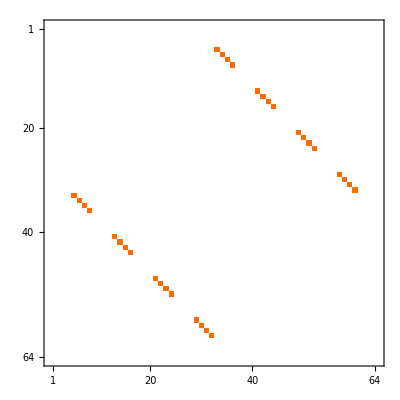

```mathematica
H2s[j_, s_, nQubit_] := FullSigma[3*(s-1)+j, 1, nQubit].FullSigma[3*s+j, 1, nQubit]+FullSigma[3*(s-1)+j, 2, nQubit].FullSigma[3*s+j, 2, nQubit]
MatrixPlot[H2s[1, 1, 6]]
```

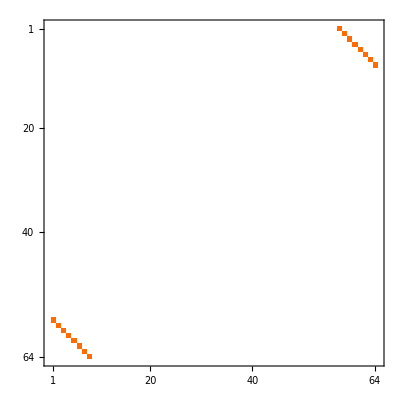

```mathematica
H3s[s_, nQubit_] := KroneckerProduct[IdentityMatrix[2^(3*(s-1))], SigmaP, SigmaP, SigmaP,IdentityMatrix[2^(nQubit-3*s)]]+KroneckerProduct[IdentityMatrix[2^(3*(s-1))], SigmaM, SigmaM, SigmaM, IdentityMatrix[2^(nQubit-3*s)]]
MatrixPlot[H3s[1, 6]]
```

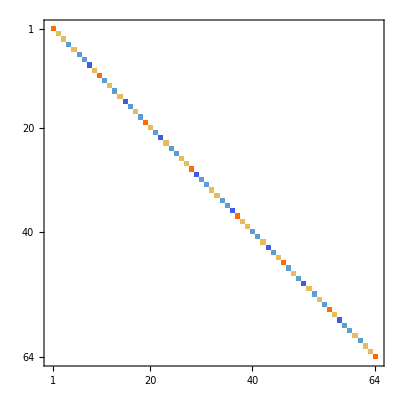

```mathematica
H1[nPlaq_] := If[nPlaq==1, 0, Sum[H1s[j, s, nPlaq*3], {j, 1, 3}, {s, 1, nPlaq-1}]]
MatrixPlot[H1[2]]
```

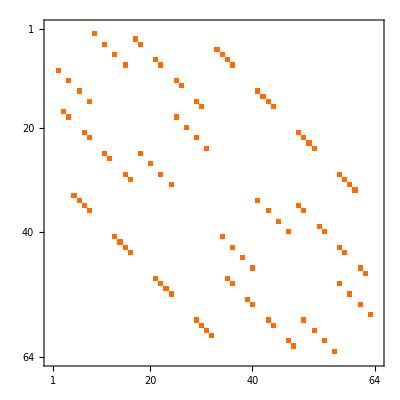

```mathematica
H2[nPlaq_] := If[nPlaq==1, 0, Sum[H2s[j, s, nPlaq*3], {j, 1, 3}, {s, 1, nPlaq-1}]]
MatrixPlot[H2[2]]
```

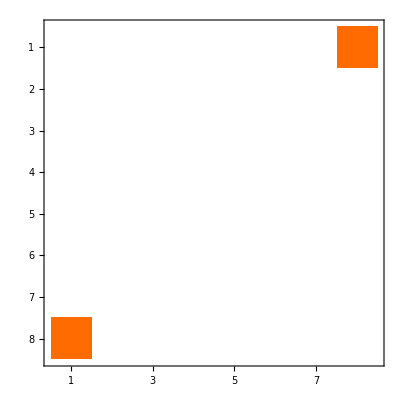

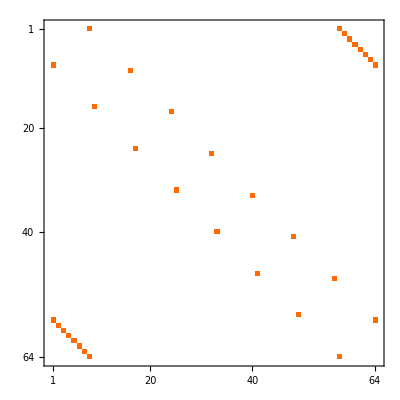

```mathematica
H3[nPlaq_] := Sum[H3s[s, nPlaq*3], {s, 1, nPlaq}]
MatrixPlot[H3[1]]
MatrixPlot[H3[2]]
```

```mathematica
H[a_, b_, c_, nPlaq_]:=a*H1[nPlaq]+b*H2[nPlaq]+c*H3[nPlaq]
```

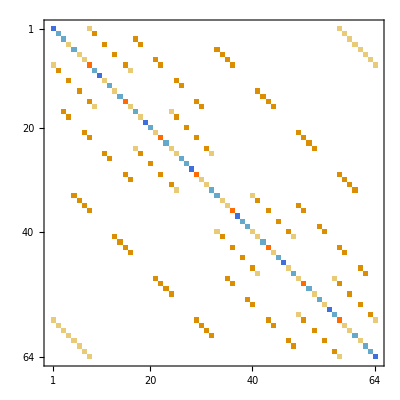

```mathematica
MatrixPlot[H[-1, 1, 1, 2]]
```

```mathematica
Eigs[a_, b_, c_, nPlaq_, k_] := Sort[Eigenvalues[H[a, b, c, nPlaq], k], Less]
Eigs[-1, 1, 1, 2, 2^6]
```

{Root-3.71Root[55-25 #1-7 #1^2+#1^3&,1]-3.714925073797535,-1-√5,-1-√5,-1-√5,-1-√5,-1-√5,-1-√5,1-√17,1-√17,1-√17,1-√17,1-√17,1-√17,-3,-3,-3,-3,-3,-3,-3,-3,-3,-3,-3,-3,-3,-3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1+√5,-1+√5,-1+√5,-1+√5,-1+√5,-1+√5,Root1.63Root[55-25 #1-7 #1^2+#1^3&,2]1.6295595051983163,5,5,5,1+√17,1+√17,1+√17,1+√17,1+√17,1+√17,Root9.09Root[55-25 #1-7 #1^2+#1^3&,3]9.085365568599219}

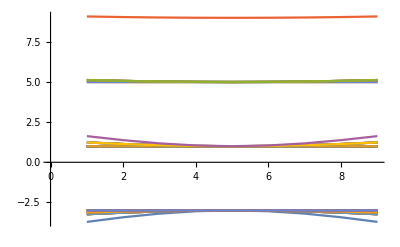

```mathematica
ListPlot[Transpose[Table[Eigs[-1, 1, c, 2, 2^6], {c, -1, 1, 0.25}]], Joined->True]
```

```mathematica
ListPlot[Transpose[Table[Eigs[-1, -1, c, 2, 2^6], {c, -1, 1, 0.25}]], Joined->True]
```

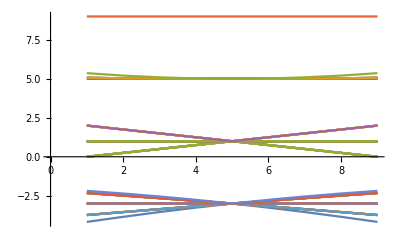

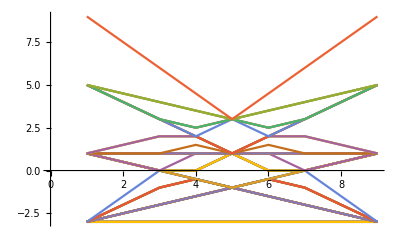

ListPlot::lpn: Transpose[{Eigenvalues[H[-1.,1.,1.,2.,64.]],Eigenvalues[H[-1.,1.,1.,3.,64.]],Eigenvalues[H[-1.,1.,1.,4.,64.]]}] is not a list of numbers or pairs of numbers.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Eigenvalues[H[-1.,1.,1.,2.,64.]],Eigenvalues[H[-1.,1.,1.,3.,64.]],Eigenvalues[H[-1.,1.,1.,4.,64.]]} cannot be transposed.

Transpose::nmtx: The first two levels of {Eigenvalues[H[-1,1,1,2,64]],Eigenvalues[H[-1,1,1,3,64]],Eigenvalues[H[-1,1,1,4,64]]} cannot be transposed.

ListPlot::lpn: Transpose[{Eigs[-1.,1.,1.,2.,64.],Eigs[-1.,1.,1.,3.,64.],Eigs[-1.,1.,1.,4.,64.]}] is not a list of numbers or pairs of numbers.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Eigs[-1.,1.,1.,2.,64.],Eigs[-1.,1.,1.,3.,64.],Eigs[-1.,1.,1.,4.,64.]} cannot be transposed.

Transpose::nmtx: The first two levels of {Eigs[-1,1,1,2,64],Eigs[-1,1,1,3,64],Eigs[-1,1,1,4,64]} cannot be transposed.

MatrixPlot::mat0: Argument H[1,1,1,2] at position 1 is not a matrix.

IdentityMatrix::dims: Dimension specification 1/2 should be a positive machine integer or a pair of positive machine integers.

```mathematica
ListPlot[Transpose[Table[Eigs[-1, b, 0, 2, 2^6], {b, -1, 1, 0.025}]], Joined->True]
```